```mathematica
dataWeek3={{1,27},{2,43},{3,54},{4,64},{5,75},{6,82},{7,84},{8,89},{9,92},{10,93},{11,97},{12,104},{13,106},{14,111},{15,116},{16,122},{17,122},{18,127},{19,128},{20,129},{21,131},{22,132},{23,134},{24,135},{25,136}}
```

{{1,27},{2,43},{3,54},{4,64},{5,75},{6,82},{7,84},{8,89},{9,92},{10,93},{11,97},{12,104},{13,106},{14,111},{15,116},{16,122},{17,122},{18,127},{19,128},{20,129},{21,131},{22,132},{23,134},{24,135},{25,136}}

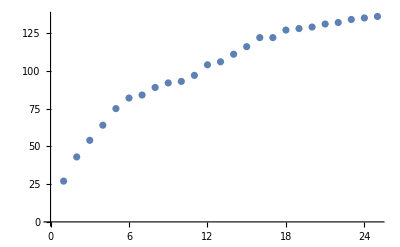

```mathematica
ListPlot[dataWeek3]
```

```mathematica
Gompertz=a*Exp[-α*Exp[-β*t]];
GompertzMakeham=a*(1-Exp[-λ*t-(α/β)*(Exp[β*t]-1)]);
```

```mathematica
gompertz=NonlinearModelFit[dataWeek3,Gompertz,{{a,139},{α,0.3},{β,0.5}},t]
```

FittedModel[140.65 ⅇ^(-1.50002 ⅇ^(«1»))]

```mathematica
gompertz["Function"]
```

140.65 ⅇ^(-1.50002 ⅇ^(-0.141582 #1))&

```mathematica
gompertz["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 140.65 | 3.34768 | 42.0141 | 1.66356×10^-22
α | 1.50002 | 0.0733906 | 20.4388 | 8.46133×10^-16
β | 0.141582 | 0.0119094 | 11.8882 | 4.75715×10^-11

```mathematica
gompertz["BestFitParameters"]
```

{a→140.65,α→1.50002,β→0.141582}

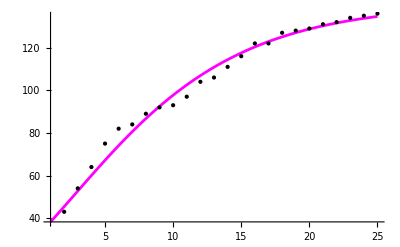

```mathematica
Plot[gompertz[t],{t,1,25},Epilog->Point[dataWeek3],PlotStyle->Magenta]
```

```mathematica
gompertz["AIC"]
```

148.691

```mathematica
gompertz["BIC"]
```

153.566

```mathematica
gompertz["RSquared"]
```

0.998555

```mathematica
gompertz["AdjustedRSquared"]
```

0.998358

```mathematica
gm=NonlinearModelFit[dataWeek3,GompertzMakeham,{{a,160},α,{λ,0.2},{β,-0.75}},t,PrecisionGoal->10]
```

FittedModel[168.029 (1-ⅇ^(0.293737 («1»)-«1»))]

```mathematica
gm["Function"]
```

101.32 (1-ⅇ^(0.0283629 (-1+ⅇ^(-2069.26 #1))-898.815 #1))&

```mathematica
gm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 168.029 | 12.5901 | 13.3461 | 1.0007×10^-11
α | 0.148747 | 0.0227301 | 6.54404 | 1.75547×10^-6
λ | 0.0573606 | 0.0139226 | 4.11997 | 0.00048773
β | -0.506395 | 0.142642 | -3.55011 | 0.00189446

```mathematica
/** β e незначим параметър за модела/
```

```mathematica
gm["BestFitParameters"]
```

{a→101.32,α→58.6901,λ→898.815,β→-2069.26}

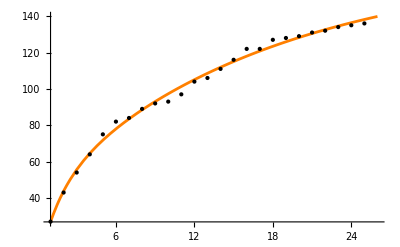

```mathematica
Plot[gm[t],{t,1,26},Epilog->Point[dataWeek3],PlotStyle->Orange]
```

```mathematica
generalGoel=NonlinearModelFit[dataWeek3,a*(1-Exp[-b*t^c]),{{a,160},b,c},t]
```

FittedModel[190.443 (1-ⅇ^(-0.167696 t^(«19»)))]

```mathematica
generalGoel["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 190.443 | 19.068 | 9.98756 | 1.2348×10^-9
b | 0.167696 | 0.0124867 | 13.43 | 4.44399×10^-12
c | 0.633089 | 0.0410005 | 15.441 | 2.73814×10^-13

```mathematica
generalGoel["BestFitParameters"]
```

{a→190.443,b→0.167696,c→0.633089}

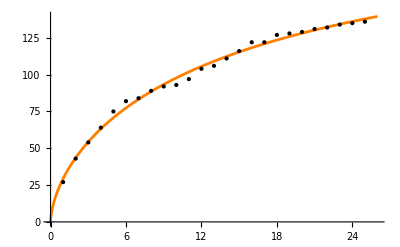

```mathematica
Plot[generalGoel[t],{t,0,26},Epilog->Point[dataWeek3],PlotStyle->Orange]
```

```mathematica
Grid[{#,generalGoel[#],gompertz[#],gm[#]}&[{"AIC","BIC","RSquared","AdjustedRSquared"}],Frame->All]
```

AIC | BIC | RSquared | AdjustedRSquared
123.546 | 128.422 | 0.999472 | 0.999399
148.691 | 153.566 | 0.998555 | 0.998358
120.739 | 126.833 | 0.999567 | 0.999484

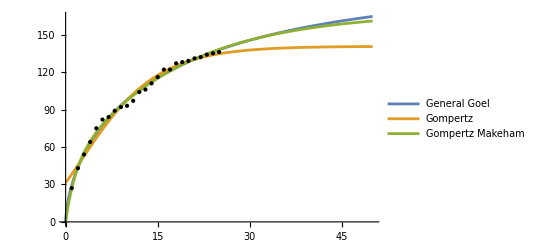

```mathematica
Plot[{generalGoel[t],gompertz[t],gm[t]},{t,0,50},PlotLegends->{"General Goel","Gompertz","Gompertz Makeham"},PlotStyle->{"red","green","blue"}, Epilog->Point[dataWeek3]]
```

```mathematica
prediction= Table[{i,Round[gm[i]]},{i,26,50}]
```

{{26,140},{27,141},{28,143},{29,144},{30,146},{31,147},{32,148},{33,149},{34,150},{35,151},{36,152},{37,153},{38,154},{39,155},{40,155},{41,156},{42,157},{43,157},{44,158},{45,159},{46,159},{47,160},{48,160},{49,160},{50,161}}

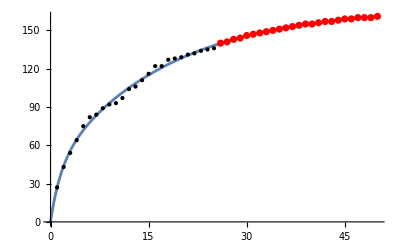

```mathematica
Show[Plot[gm[t],{t,0,50},Epilog->Point[dataWeek3]],ListPlot[prediction,PlotStyle->Red]]
```